```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{Eb e[t]+tau (Es+Eb) D[e[t],t]==sg0,e'[Infinity]==0},e,t]
```

DSolve::bvlim: For some branches of the general solution, unable to compute the limit at the given points. Some of the solutions may be lost.

{}

```mathematica
DSolve[{tau D[sg[t],t]+sg[t]==sg0,sg'[0]==0},sg,t]
```

{{sg→Function[{t},sg0]}}

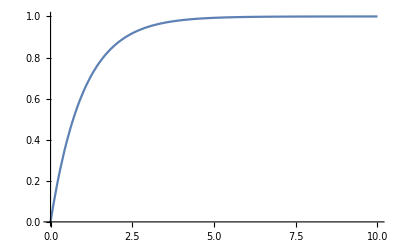

```mathematica
Plot[1-Exp[-t],{t,0,10},PlotRange->All]
```